```mathematica
cosx[x_]=0.5-(4/Pi^2)*∑_(n=0)^∞ Cos[(2*n+1)*Pi*x]/(2*n+1)^2
```

0.5-(ⅇ^(-ⅈ π x) (LerchPhi[ⅇ^(-2 ⅈ π x),2,1/2]+ⅇ^(2 ⅈ π x) LerchPhi[ⅇ^(2 ⅈ π x),2,1/2]))/(2 π^2)

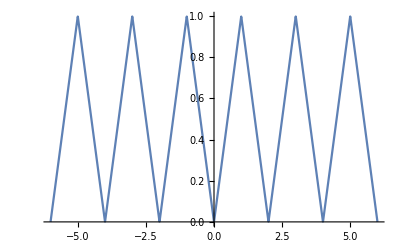

```mathematica
Plot[cosx[x],{x,-6,6}]
```

```mathematica
sinx[x_]=(2/Pi)*∑_(n=1)^∞ (Sin[n*Pi*x]*(-1)^(n+1))/n
```

(ⅈ (-Log[1+ⅇ^(ⅈ π x)]+Log[ⅇ^(-ⅈ π x) (1+ⅇ^(ⅈ π x))]))/π

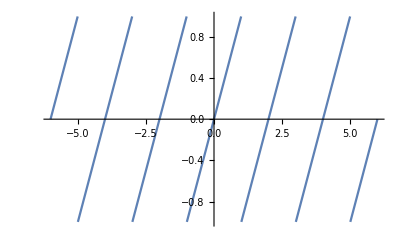

```mathematica
Plot[sinx[x],{x,-6,6}]
```

```mathematica
halfsinx[x_]=(8/Pi^2)*∑_(n=0)^∞ ((-1)^n)*Sin[(2*n+1)*Pi*x/2]/(2*n+1)^2
```

-(ⅈ ⅇ^(-1/2 ⅈ π x) (-LerchPhi[-ⅇ^(-ⅈ π x),2,1/2]+ⅇ^(ⅈ π x) LerchPhi[-ⅇ^(ⅈ π x),2,1/2]))/π^2

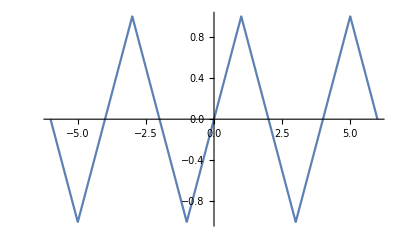

```mathematica
Plot[halfsinx[x],{x,-6,6}]
```